# MSTW PDF example code

Clear all definitions.

```mathematica
Clear["Global`*"]
```

Load Mathematica package containing global variables and functions to access grids.
Change the pdfpath to the location where the mstwpdf.m file is stored.

```mathematica
pdfpath="/home/watt/MSTW/Public/";
SetDirectory[pdfpath];
```

```mathematica
<<mstwpdf.m
```

Mathematica package for MSTW PDFs
by Graeme Watt <watt(at)hep.ucl.ac.uk>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
?ReadPDFGrid
```

The function ReadPDFGrid[prefix,ih] reads the PDF grid corresponding to eigenvector set ih, where ih=0 is the central set, into memory from the location specified by prefix.

```mathematica
?xf
```

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f, that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

## Use of the central PDF set

The prefix should be set to the location of the grid files.

```mathematica
prefix=pdfpath<>"Grids/mstw2008nnlo";
Timing[ReadPDFGrid[prefix,0]]
```

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.00.dat

{10.0825,Null}

Write out the central PDFs for a fixed momentum scale x and scale q.

```mathematica
ih=0;x=1.*^-3;q=10.;
upv=xf[ih,x,q,8]
dnv=xf[ih,x,q,7]
usea=xf[ih,x,q,-2]
dsea=xf[ih,x,q,-1]
str=xf[ih,x,q,3]
sbar=xf[ih,x,q,-3]
chm=xf[ih,x,q,4]
cbar=xf[ih,x,q,-4]
bot=xf[ih,x,q,5]
bbar=xf[ih,x,q,-5]
glu=xf[ih,x,q,0]
phot=xf[ih,x,q,13]
```

0.063418

0.028302

0.967482

0.968758

0.80936

0.811037

0.56906

0.568904

0.22973

0.229703

16.795

0.

Clear the above definitions.

```mathematica
Clear[ih,x,q,upv,dnv,usea,dsea,str,sbar,chm,cbar,bot,bbar,glu,phot];
```

Check that the number and momentum sum rules are satisfied to reasonable accuracy.  (Note that cv = c - cbar and bv = b - bbar are only non-zero at NNLO.)

```mathematica
NIntegrate[xf[0,x,10.,7]/x,{x,1.*^-9,1.},MaxRecursion->100](* dv integrated over x: should be 1 *)
```

0.995442

```mathematica
NIntegrate[xf[0,x,10.,8]/x,{x,1.*^-9,1.},MaxRecursion->100](* uv integrated over x: should be 2 *)
```

1.99542

```mathematica
NIntegrate[xf[0,x,10.,9]/x,{x,1.*^-9,1.},MaxRecursion->100](* sv integrated over x: should be zero *)
```

0.00137195

```mathematica
NIntegrate[xf[0,x,10.,10]/x,{x,1.*^-9,1.},MaxRecursion->100](* cv integrated over x: should be zero *)
```

-0.000478829

```mathematica
NIntegrate[xf[0,x,10.,11]/x,{x,1.*^-9,1.},MaxRecursion->100](* bv integrated over x: should be zero *)
```

-0.0000833498

```mathematica
NIntegrate[xf[0,x,10.,9],{x,1.*^-6,1.},MaxRecursion->100](* xsv integrated over x: should be non-zero *)
```

0.00132608

```mathematica
NIntegrate[xf[0,x,10.,10],{x,1.*^-6,1.},MaxRecursion->100](* xcv integrated over x: should be non-zero only at NNLO *)
```

-0.0000723831

```mathematica
NIntegrate[xf[0,x,10.,11],{x,1.*^-6,1.},MaxRecursion->100](* xbv integrated over x: should be non-zero only at NNLO *)
```

-0.0000127134

```mathematica
NIntegrate[Sum[xf[0,x,q,f]/.{q->10.},{f,-6,6}],{x,1.*^-6,1.},MaxRecursion->100] (* momentum sum rule: should be 1 *)
```

0.999529

Plot the valence quark distributions of the central set.
(Note that cv = c - cbar and bv = b - bbar are only non-zero at NNLO.)

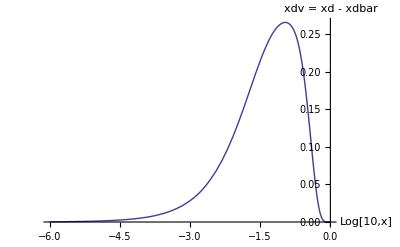

```mathematica
Plot[xf[0,10.^ix,q,7]/.{q->10.},{ix,-6,0},AxesLabel->{"Log[10,x]","xdv = xd - xdbar"}]
```

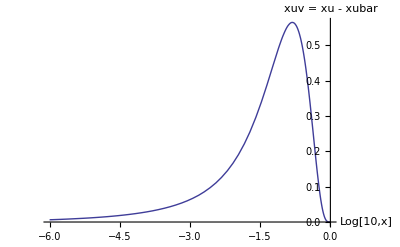

```mathematica
Plot[xf[0,10.^ix,q,8]/.{q->10.},{ix,-6,0},PlotRange->All,AxesLabel->{"Log[10,x]","xuv = xu - xubar"}]
```

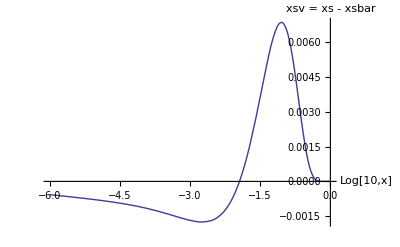

```mathematica
Plot[xf[0,10.^ix,q,9]/.{q->10.},{ix,-6,0},AxesLabel->{"Log[10,x]","xsv = xs - xsbar"}]
```

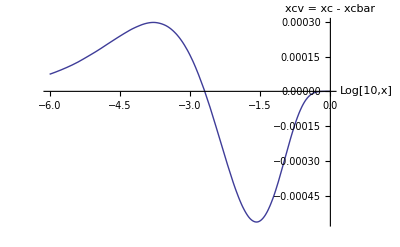

```mathematica
Plot[xf[0,10.^ix,q,10]/.{q->10.},{ix,-6,0},AxesLabel->{"Log[10,x]","xcv = xc - xcbar"}]
```

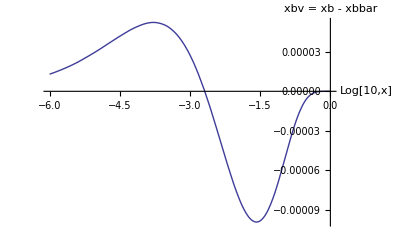

```mathematica
Plot[xf[0,10.^ix,q,11]/.{q->10.},{ix,-6,0},AxesLabel->{"Log[10,x]","xbv = xb - xbbar"}]
```

## Use of the eigenvector PDF sets

```mathematica
?distance
```

Distance along a particular eigenvector direction (t).

```mathematica
?tolerance
```

Square root of the change in the global chi-squared (T) obtained by moving a distance t along a particular eigenvector direction.  Under ideal quadratic behaviour, t = T.

Get the central value of the gluon distribution.￿

```mathematica
ih=0;x=1.*^-3;q=10.;
glu=xf[ih,x,q,0]
distance
tolerance
```

16.795

0.

0.

Now get the value of the gluon distribution at a distance t from the global minimum along the first eigenvector direction in the '+' direction.  The distance t is chosen to give a tolerance T ensuring all data sets are described within their 90% confidence level (C.L.) limits.

```mathematica
ReadPDFGrid[prefix<>".90cl",1]
glu=xf[1,x,q,0]
distance
tolerance
```

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.01.dat

16.367

7.87229

8.38381

Now the same thing, but with the tolerance chosen to ensure that all data sets are described only within their one-sigma (68%) C.L. limits.

```mathematica
ReadPDFGrid[prefix<>".68cl",1]
glu=xf[1,x,q,0]
distance
tolerance
```

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.68cl.01.dat

16.6

3.60452

3.71481

```mathematica
Clear[ih,x,q,glu];
```

```mathematica
?nhess
nhess
```

The number of eigenvector PDF sets.

40

Load the eigenvector sets into memory.  Choose either the 90% C.L. or the 68% C.L. sets.  Warning : the next line will take a long time to evaluate!  (For an estimate look at the time taken to read the central fit above and multiply by nhess.)

```mathematica
Timing[Do[ReadPDFGrid[prefix<>".90cl",ih],{ih,1,nhess}]]
```

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.01.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.02.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.03.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.04.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.05.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.06.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.07.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.08.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.09.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.10.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.11.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.12.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.13.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.14.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.15.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.16.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.17.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.18.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.19.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.20.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.21.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.22.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.23.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.24.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.25.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.26.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.27.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.28.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.29.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.30.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.31.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.32.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.33.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.34.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.35.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.36.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.37.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.38.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.39.dat

PDF grid read from /home/watt/MSTW/Public/Grids/mstw2008nnlo.90cl.40.dat

{416.509,Null}

Define functions to give the uncertainty on the parton distributions using both the formula for asymmetric errors [eqs.(51,52) of arXiv:0901.0002] ￿and the formula for symmetric errors [eq.(50) of same paper].￿

```mathematica
delp[x_Real,q_Real,f_Integer]:=Sqrt[Sum[Max[xf[2i-1,x,q,f]-xf[0,x,q,f],xf[2i,x,q,f]-xf[0,x,q,f],0.]^2,{i,1,nhess/2}]]
delm[x_Real,q_Real,f_Integer]:=Sqrt[Sum[Max[xf[0,x,q,f]-xf[2i-1,x,q,f],xf[0,x,q,f]-xf[2i,x,q,f],0.]^2,{i,1,nhess/2}]]
del[x_Real,q_Real,f_Integer]:=0.5*Sqrt[Sum[(xf[2i-1,x,q,f]-xf[2i,x,q,f])^2,{i,1,nhess/2}]]
```

Plot gluon distribution with uncertainty band at 10 GeV.
(The Plot option Filling requires Mathematica 6.)

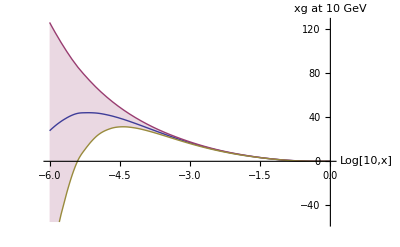

```mathematica
Plot[Evaluate[{xf[0,x,q,f],xf[0,x,q,f]+delp[x,q,f],xf[0,x,q,f]-delm[x,q,f]}/.{q->10.,x->10.^ix,f->0}],{ix,-6,0},AxesLabel->{"Log[10,x]","xg at 10 GeV"},Filling->{2->{3}}]
```

Plot fractional uncertainty in gluon distribution at 10 GeV.
(The Plot option "Filling" requires Mathematica 6.)

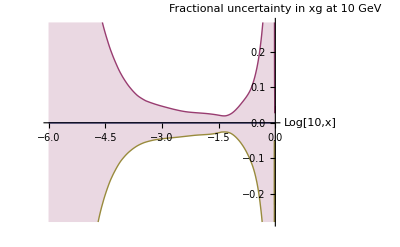

```mathematica
Plot[Evaluate[{0.,delp[x,q,f]/xf[0,x,q,f],-delm[x,q,f]/xf[0,x,q,f]}/.{q->10.,x->10.^ix,f->0}],{ix,-6,0},AxesLabel->{"Log[10,x]","Fractional uncertainty in xg at 10 GeV"},Filling->{2->{3}}]
```

Define a function to convert a real number to equivalent of "1PE12.4" Fortran format or￿"%12.4E" C format.

```mathematica
format[number_Real]:=ToString[ScientificForm[number,10,NumberFormat->(ToString[PaddedForm[ToExpression[#1],{6,4}]]<>"E"<>ToString[PaddedForm[If[Head[ToExpression[#3]]==Integer,ToExpression[#3],0,0],2,NumberPadding->{"0",""},SignPadding->True,NumberSigns->{"-","+"}]]&)]]
```

Define a function to pad a string to a certain length.

```mathematica
PadString[str_String,len_Integer]:=Module[{temp=str},While[StringLength[temp]<len,temp=" "<>temp]; Return[temp];]
```

Define a function to write the PDFs as a function of x to a file at a fixed value of q.
Extrapolation will be used for x < 10^-6.￿

```mathematica
WritePDFvsX[q_Real,f_Integer]:=Module[{flavours,ix,nx=100,xmin=1.*^-7,xmax=0.99,x,line},
flavours={"bbar","cbar","sbar","ubar","dbar","glu", "dn","up","str","chm","bot"};
filename="x"<>flavours[[f+6]]<>"_vs_x_math.dat";
file=OpenWrite[filename];
WriteString[file," # q = "<>format[q]<>"\n"];
WriteString[file," #"<>PadString["x",10]<>PadString["x"<>flavours[[f+6]],12]<>PadString["error+",12]<>PadString["error-",12]<>PadString["error",12]<>"\n"];
Do[{x=10.^(Log[10,xmin]+(ix-1.)/(nx-1.)*(Log[10,xmax]-Log[10,xmin]));
line=format[x]<>format[xf[0,x,q,f]]<>format[delp[x,q,f]]<>format[delm[x,q,f]]<>format[del[x,q,f]]<>"\n";
WriteString[file,line];
},{ix,1,nx}];
Close[file];
Print["x"<>flavours[[f+6]]," vs. x for q2 = ",q^2," written to ",filename];
]
```

```mathematica
Do[WritePDFvsX[q,f]/.{q->10.},{f,-5,5}]
```

xbbar vs. x for q2 = 100. written to xbbar_vs_x_math.dat

xcbar vs. x for q2 = 100. written to xcbar_vs_x_math.dat

xsbar vs. x for q2 = 100. written to xsbar_vs_x_math.dat

xubar vs. x for q2 = 100. written to xubar_vs_x_math.dat

xdbar vs. x for q2 = 100. written to xdbar_vs_x_math.dat

xglu vs. x for q2 = 100. written to xglu_vs_x_math.dat

xdn vs. x for q2 = 100. written to xdn_vs_x_math.dat

xup vs. x for q2 = 100. written to xup_vs_x_math.dat

xstr vs. x for q2 = 100. written to xstr_vs_x_math.dat

xchm vs. x for q2 = 100. written to xchm_vs_x_math.dat

xbot vs. x for q2 = 100. written to xbot_vs_x_math.dat

Define a function to write the PDFs as a function of q^2 to a file at a fixed value of x.
Extrapolation will be used for q^2 < 1 GeV^2 and for q^2 > 10^9 GeV^2.￿

```mathematica
WritePDFvsQ2[x_Real,f_Integer]:=Module[{flavours,iq,nq=100,q2min=0.5,q2max=1.*^10,q,line},
flavours={"bbar","cbar","sbar","ubar","dbar","glu", "dn","up","str","chm","bot"};
filename="x"<>flavours[[f+6]]<>"_vs_q2_math.dat";
file=OpenWrite[filename];
WriteString[file," # x = "<>format[x]<>"\n"];
WriteString[file," #"<>PadString["q2",10]<>PadString["x"<>flavours[[f+6]],12]<>PadString["error+",12]<>PadString["error-",12]<>PadString["error",12]<>"\n"];
Do[{q=Sqrt[10.^(Log[10,q2min]+(iq-1.)/(nq-1.)*(Log[10,q2max]-Log[10,q2min]))];
line=format[q^2]<>format[xf[0,x,q,f]]<>format[delp[x,q,f]]<>format[delm[x,q,f]]<>format[del[x,q,f]]<>"\n";
WriteString[file,line];
},{iq,1,nq}];
Close[file];
Print["x"<>flavours[[f+6]]," vs. q2 for x = ",x," written to ",filename];
]
```

```mathematica
Do[WritePDFvsQ2[x,f]/.{x->1.*^-3},{f,-5,5}]
```

xbbar vs. q2 for x = 0.001 written to xbbar_vs_q2_math.dat

xcbar vs. q2 for x = 0.001 written to xcbar_vs_q2_math.dat

xsbar vs. q2 for x = 0.001 written to xsbar_vs_q2_math.dat

xubar vs. q2 for x = 0.001 written to xubar_vs_q2_math.dat

xdbar vs. q2 for x = 0.001 written to xdbar_vs_q2_math.dat

xglu vs. q2 for x = 0.001 written to xglu_vs_q2_math.dat

xdn vs. q2 for x = 0.001 written to xdn_vs_q2_math.dat

xup vs. q2 for x = 0.001 written to xup_vs_q2_math.dat

xstr vs. q2 for x = 0.001 written to xstr_vs_q2_math.dat

xchm vs. q2 for x = 0.001 written to xchm_vs_q2_math.dat

xbot vs. q2 for x = 0.001 written to xbot_vs_q2_math.dat

## Mathlink interface to Fortran code for α_S

Values of mCharm, mBottom, alphaSQ0, alphaSMZ, alphaSorder,alphaSnfmax are filled when the ReadPDFGrid function is called.

```mathematica
?mCharm
mCharm
```

Charm quark mass in GeV.

1.4

```mathematica
?mBottom
mBottom
```

Bottom quark mass in GeV.

4.75

```mathematica
?alphaSQ0
alphaSQ0
```

Value of alphaS at Q0 = 1 GeV.

0.45077

```mathematica
?alphaSMZ
alphaSMZ
```

Value of alphaS at the Z mass.

0.11707

```mathematica
?alphaSorder
alphaSorder
```

Perturbative order of alphaS:  0=LO, 1=NLO, 2=NNLO.

2

```mathematica
?alphaSnfmax
alphaSnfmax
```

Maximum number of flavours in alphaS evolution.

5

Install Mathematica definitions to call Fortran code for alphaS via Mathlink interface.
Requires the binary alphaS.exe to be compiled from alphaS.c, alphaS.tm and alphaS.f.  Under Linux, do this with "mcc -o alphaS.exe alphaS.c alphaS.tm alphaS.f -lg2c".

```mathematica
Install["alphaS.exe"]
```

LinkObject[./alphaS.exe,7,7]

```mathematica
?InitAlphaS
```

The function InitAlphaS[IORD,FR2,MUR,ASMUR,MC,MB,MT] initialises the AlphaS function at perturbative order set to IORD (0=LO, 1=NLO, 2=NNLO), with the ratio of mu_f^2 to mu_r^2 set to FR2, input mu_r in GeV set to MUR, input value of alpha_s at mu_r = MUR set to ASMUR, with flavour transitions when the factorisation scale equals the heavy quark pole masses MC, MB and MT.

```mathematica
InitAlphaS[alphaSorder,1.,1.,alphaSQ0,mCharm,mBottom,1.*^10]
```

```mathematica
?AlphaS
```

The function AlphaS[MUR] returns the value of the running strong coupling at a renormalisation scale in GeV of MUR.  A call to InitAlphaS should previously have been made.

```mathematica
AlphaS[1.]
```

0.45077

```mathematica
AlphaS[91.1876]
```

0.11707

Alternatively, initialise alphaS at the Z mass.

```mathematica
InitAlphaS[alphaSorder,1.,91.1876,alphaSMZ,mCharm,mBottom,1.*^10]
```

```mathematica
AlphaS[91.1876]
```

0.11707

```mathematica
AlphaS[1.]
```

0.450772

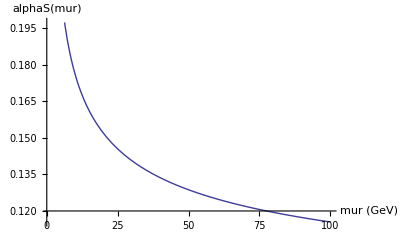

```mathematica
Plot[AlphaS[mur],{mur,1,100},AxesLabel->{"mur (GeV)","alphaS(mur)"}]
```